# DIFFERENTIAL EQUATIONS PRACTICAL

## Name: Om Gupta Roll No.: 21078570037

1.	Find the solutions of the first order differential equation
	y’ = (x+y)/(x-y)

Given equation,

```mathematica
eqn1 = y'[x]==(x+y[x])/(x-y[x]);
```

Solution,

```mathematica
sol1 = DSolve[eqn1,y[x],x]
```

Solve[-ArcTan[y[x]/x]+1/2 Log[1+y[x]^2/x^2]==C[1]-Log[x],y[x]]

2.	Solve the following second order differential equation. Also plot the particular solution for arbitrary values of constants.
	y’’+y=sinx

Given equation,

```mathematica
eqn2 = y''[x]+y[x]==Sin[x];
```

Solution,

```mathematica
sol2 = DSolve[eqn2, y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]+1/4 (-2 x Cos[x]-2 Cos[x]^2 Sin[x]+Cos[x] Sin[2 x])}}

Now, plot of particular solution for arbitrary values of constans, c_1= 2  and c_2 = -2:

```mathematica
sol2plot1 = y[x]/.sol2/.{C[1]->2,C[2]->-2};
```

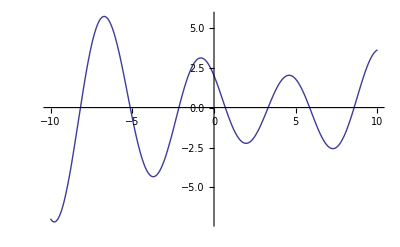

```mathematica
Plot[sol2plot1,{x,-10,10}]
```

3.	Solve the following non-homogenous ODE using method of variation of parameters
	y’’ - 2y’ + y = e^xsinx

Given equation,

```mathematica
eqn3 = y''[x]-2y'[x]+y[x]==Exp[x]Sin[x];
```

Solution,

```mathematica
sol3 = DSolve[eqn3,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^x x C[2]-ⅇ^x Sin[x]}}

4.	Find the general solution of the following system of equations:
	x’(t) + y(t) = 0
	y’(t) + x(t) = 0

Given equations,

```mathematica
eqn4a = x'[t]+y[t]==0;
```

```mathematica
eqn4b = y'[t]+x[t]==0;
```

Solution,

```mathematica
sol4 = DSolve[{eqn4a,eqn4b},{x[t],y[t]},t]
```

{{x[t]→1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2],y[t]→-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[2]}}

5.	Solve the following partial differential equation
	yU_x + xU_y  = 0

Given equation,

```mathematica
eqn5 = y*D[u[x,y],x]+x*D[u[x,y],y]==0;
```

Solution,

```mathematica
sol5 = DSolve[eqn5,u[x,y],{x,y}]
```

{{u[x,y]→C[1][1/2 (-x^2+y^2)]}}

Now, plot of characteristic equation:

```mathematica
Plot3D[u[x,y]/.sol5/.C[1][a_]->sin[a],{x,-10,10},{y,-10,10}]
```

-Graphics3D-